```mathematica
maxHCalcImp[x_,imp_,f_,βp_]:=
Module[{h,m,v,t,tsnond,nondeqnsb,nondbcsb,solb,nondeqnsc,nondbcsc,solc,dom,maxh},

tsnond := N[imp/f];

(*Solve boost phase*)
nondeqnsb={h'[t] == v[t],
 v'[t] == (f-x*Exp[-βp h[t]]*v[t]^2)/m[t] - 1, 
m'[t] == -f};

nondbcsb = {h[0] == 0, v[0] ==0, m[0] == 1};

solb=Evaluate[NDSolve[({nondeqnsb, nondbcsb})//Flatten,{h[t],v[t],m[t]},{t, 0.0, tsnond}]];

(*Solve coast phase*)
nondeqnsc={h'[t] == v[t],
 v'[t] == (-x*Exp[-βp h[t]]*v[t]^2)/m[t] - 1, 
m'[t] == 0};

nondbcsc = {h[tsnond]== solb[[1]][[1]][[2]][[0]][tsnond],
v[tsnond]== solb[[1]][[2]][[2]][[0]][tsnond],
m[tsnond]== solb[[1]][[3]][[2]][[0]][tsnond]};

solc=Evaluate[Quiet[NDSolve[{nondeqnsc, nondbcsc}//Flatten,{h[t],v[t],m[t]},{t,  tsnond, 20*tsnond}]]];
(*Find apogee*)
dom=solc[[1]][[1]][[2]][[0]]["Domain"][[1]];
maxh=FindMaxValue[{solc[[1]][[1]][[2]],dom[[1]]<t<dom[[2]]},t]]
```

```mathematica
maxHCalcImpwithPlot[x_,imp_,f_,βp_]:=
Module[{h,m,v,t,nondeqnsb,nondbcsb,nondeqnsc,nondbcsc,maxh},

tsnond = imp/f;

(*Solve boost phase*)
nondeqnsb={h'[t] == v[t],
 v'[t] == (f-x*Exp[-βp h[t]]*v[t]^2)/m[t] - 1, 
m'[t] == -f};

nondbcsb = {h[0] == 0, v[0] ==0, m[0] == 1};

solb=Evaluate[NDSolve[({nondeqnsb, nondbcsb})//Flatten,{h[t],v[t],m[t]},{t, 0.0, tsnond}]];

(*Solve coast phase*)
nondeqnsc={h'[t] == v[t],
 v'[t] == (-x*Exp[-βp h[t]]*v[t]^2)/m[t] - 1, 
m'[t] == 0};

nondbcsc = {h[tsnond]== solb[[1]][[1]][[2]][[0]][tsnond],
v[tsnond]== solb[[1]][[2]][[2]][[0]][tsnond],
m[tsnond]== solb[[1]][[3]][[2]][[0]][tsnond]};

solc=Evaluate[Quiet[NDSolve[{nondeqnsc, nondbcsc}//Flatten,{h[t],v[t],m[t]},{t,  tsnond, 20*tsnond}]]];


(*Find apogee*)
dom=solc[[1]][[1]][[2]][[0]]["Domain"][[1]];

g1=Plot[ (h[t]/.solb[[1]]),{t,0,tsnond},PlotStyle->Red];
g2=Plot[ (h[t]/.solc[[1]]),{t,dom[[1]], dom[[2]]}];

maxh=FindMaxValue[{solc[[1]][[1]][[2]],dom[[1]]<t<dom[[2]]},t]]
```

```mathematica
(*Based on McGill, Team 47 , 2018*)
x = (1/2)*1.225*2000^2*0.5*(π*(2.5*25.4/1000)^2)/(24*10)
mr = 3547/24270//N
tw =  8.8
maxHCalcImpwithPlot[x, mr,tw, 50]
g3=Plot[(c^2/g)*solb[[1]][[1]][[2]][[0]][t/(c/g)]/.{c-> 2000, g-> 10},{t, 0, tsnond*200},PlotStyle-> Red,PlotRange->All] ;
g4=Plot[(c^2/g)*solc[[1]][[1]][[2]][[0]][t/(c/g)]/.{c-> 2000, g-> 10},{t, tsnond*200,dom[[2]]*200}] ;
Show[{g3,g4},PlotRange->{0, All}]
g5=Plot[c*solb[[1]][[2]][[2]][[0]][t/(c/g)]/.{c-> 2000, g-> 10},{t, 0, tsnond*200}] ;
g6=Plot[c*solc[[1]][[2]][[2]][[0]][t/(c/g)]/.{c-> 2000, g-> 10},{t, tsnond*200,20*tsnond*200}] ;
Show[{g5,g6},PlotRange-> {0,All}]
```

64.658

0.146148

8.8

0.00709512

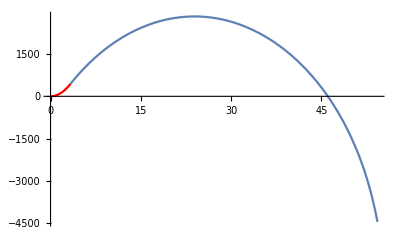
```mathematica
gmcgill=-Graphics-
```

-Graphics-

34.4843

0.27972

1.51515

0.0163138

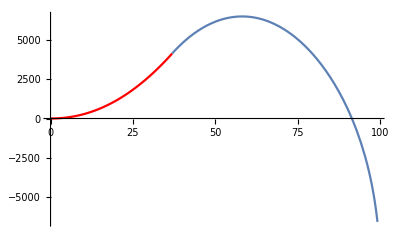

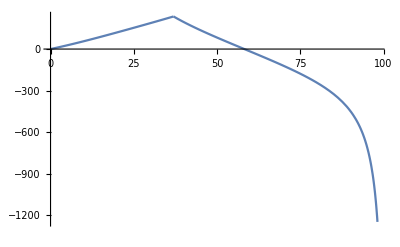

```mathematica
(*Based on Waterloo, Team 38 , 2018*)
x = (1/2)*1.225*2000^2*0.5*(π*(3*25.4/1000)^2)/(64.8*10)
mr = 40/143//N
tw =1000/660//N
maxHCalcImpwithPlot[x, mr,tw, 50]
g3=Plot[(c^2/g)*solb[[1]][[1]][[2]][[0]][t/(c/g)]/.{c-> 2000, g-> 10},{t, 0, tsnond*200},PlotStyle-> Red,PlotRange->All] ;
g4=Plot[(c^2/g)*solc[[1]][[1]][[2]][[0]][t/(c/g)]/.{c-> 2000, g-> 10},{t, tsnond*200,dom[[2]]*200}] ;
Show[{g3,g4},PlotRange->{0, All}]
g5=Plot[c*solb[[1]][[2]][[2]][[0]][t/(c/g)]/.{c-> 2000, g-> 10},{t, 0, tsnond*200}] ;
g6=Plot[c*solc[[1]][[2]][[2]][[0]][t/(c/g)]/.{c-> 2000, g-> 10},{t, tsnond*200,dom[[2]]*200}] ;
Show[{g5,g6},PlotRange-> {0,All}]
```

```mathematica
gwaterloo=-Graphics-
```

-Graphics-

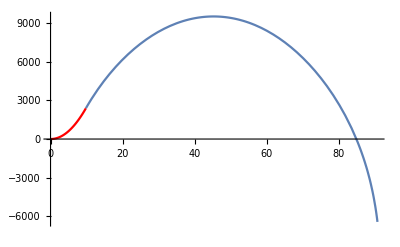
```mathematica
gwaterloo=-Graphics-
```

-Graphics-

```mathematica
(*Based on UCLA, Team 108 , 2018*)
x = (1/2)*1.225*2000^2*0.5*(π*(3*25.4/1000)^2)/(26.7*10)
mr = 1-46.2/58.8//N
tw =500/58.8
maxHCalcImpwithPlot[x, mr,tw, 50]
g3=Plot[(c^2/g)*solb[[1]][[1]][[2]][[0]][t/(c/g)]/.{c-> 2000, g-> 10},{t, 0, tsnond*200},PlotStyle-> Red,PlotRange->All] ;
g4=Plot[(c^2/g)*solc[[1]][[1]][[2]][[0]][t/(c/g)]/.{c-> 2000, g-> 10},{t, tsnond*200,dom[[2]]*200}] ;
Show[{g3,g4},PlotRange->{0, All}]
g5=Plot[c*solb[[1]][[2]][[2]][[0]][t/(c/g)]/.{c-> 2000, g-> 10},{t, 0, tsnond*200}] ;
g6=Plot[c*solc[[1]][[2]][[2]][[0]][t/(c/g)]/.{c-> 2000, g-> 10},{t, tsnond*200,20*tsnond*200}] ;
Show[{g5,g6},PlotRange-> {0,All}]
```

83.6921

0.214286

8.5034

0.0107077

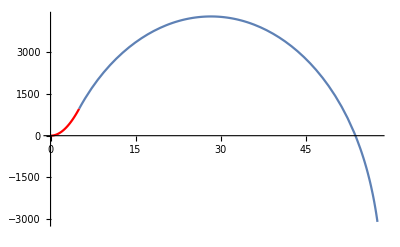
```mathematica
gucla=-Graphics-
```

-Graphics-

{0,0.005,0.0075,0.01,0.015,0.02,0.025,0.03,0.035,0.04,0.045,0.05}

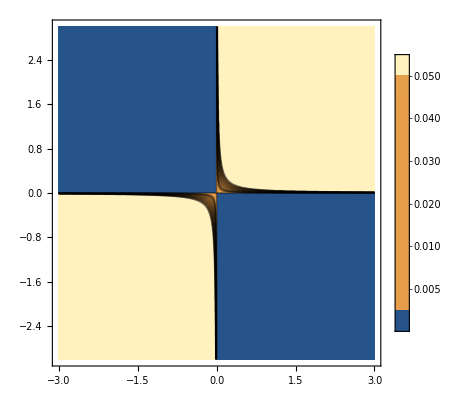

```mathematica
conts = {0,0.005, 0.0075, 0.01, 0.015, 0.02,0.025, 0.03 ,0.035,0.04,0.045,0.05}
ContourPlot[x y,{x,-3,3},{y,-3,3},Contours-> conts,PlotLegends->Automatic]
```

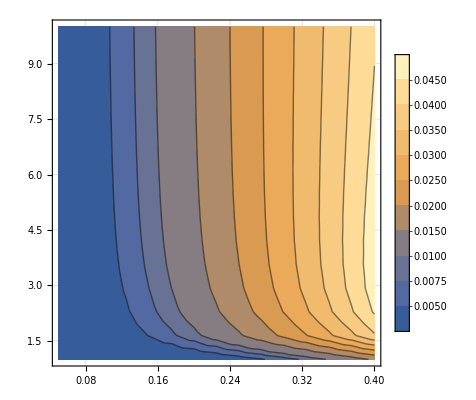

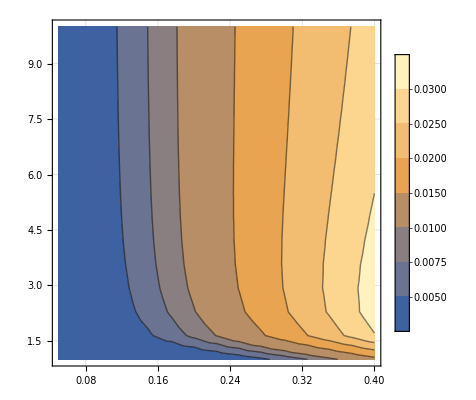

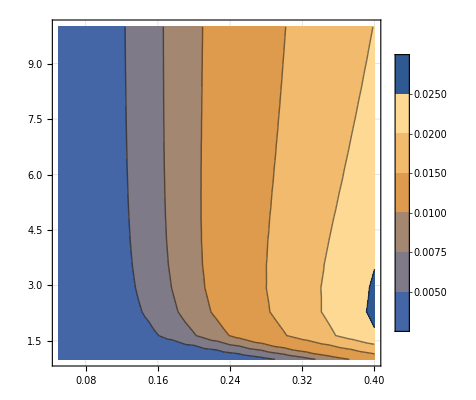

```mathematica
ContourPlot[maxHCalcImp[30, imp,f,50],{imp,0.05,0.4},{f,1,10},MaxRecursion->0,GridLines->Automatic,PlotLegends->Automatic,Contours->conts]
ContourPlot[maxHCalcImp[60, imp,f,50],{imp,0.05,0.4},{f,1,10},MaxRecursion->0,GridLines->Automatic,PlotLegends->Automatic,Contours->conts]
ContourPlot[maxHCalcImp[90, imp,f,50],{imp,0.05,0.4},{f,1,10},MaxRecursion->0,GridLines->Automatic,PlotLegends->Automatic,Contours->conts]
```

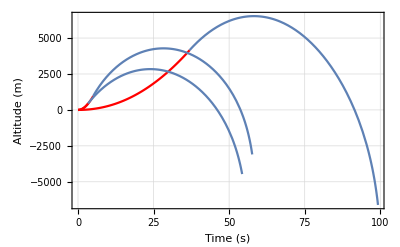

```mathematica
Show[{gwaterloo,gucla,gmcgill},PlotRange->{0, All}, GridLines-> Automatic,Frame-> True, FrameLabel-> {"Time (s)", "Altitude (m)"}]
```

```mathematica
xfunc[m_]:=(1/2)*1.225*2000^2*0.5*(π*(3*25.4/1000)^2)/(m*10)
thrust[m_,tw_]:=tw*m*10
```

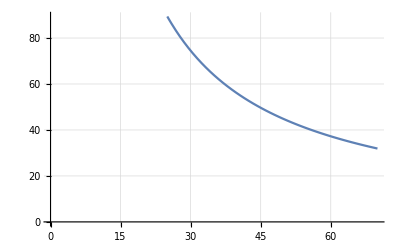

```mathematica
Plot[xfunc[m],{m,25,70},AxesOrigin->{0,0},GridLines->Automatic]
```

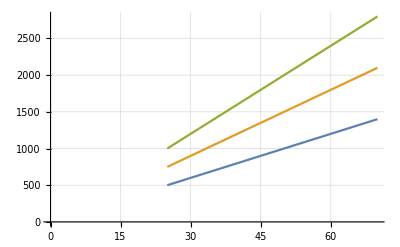

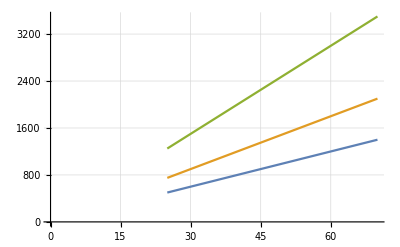

```mathematica
Plot[{thrust[m,2],thrust[m,3],thrust[m,4]},{m,25,70},AxesOrigin->{0,0},GridLines->Automatic]
```

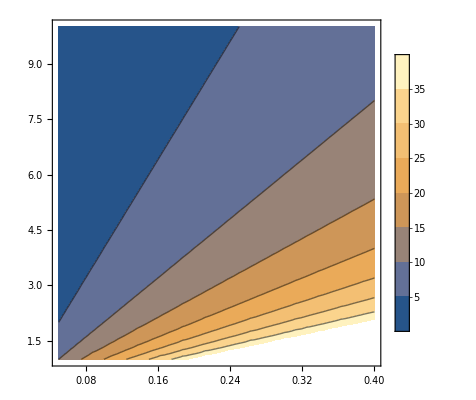

```mathematica
ContourPlot[{imp/f*200},{imp,0.05, 0.4},{f,1,10},PlotLegends->Automatic]
```